```mathematica
ClearAll["Global`*"]
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out","vortexMerge"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/vortexMerge

```mathematica
srts256 = Complement[FileNames["*size256"], FileNames["*time"], FileNames["cumulant*"]];
cumulants256 = Complement[FileNames["*size256"], FileNames["*time"], FileNames["srt*"]];srts128 = Complement[FileNames["*size128"], FileNames["*time"], FileNames["cumulant*"]];
cumulants128 = Complement[FileNames["*size128"], FileNames["*time"], FileNames["srt*"]];srts96 = Complement[FileNames["*size96"], FileNames["*time"], FileNames["cumulant*"]];
cumulants96 = Complement[FileNames["*size96"], FileNames["*time"], FileNames["srt*"]];

getReynolds[thelist_]:=Read[StringToStream[#],Number]&/@ Flatten[ StringDrop[#,2] &/@StringCases[thelist, RegularExpression["Re([0-9]*)"]]]

srts256 = srts256[[Ordering[getReynolds[srts256]]]];
cumulants256 = cumulants256[[Ordering[getReynolds[cumulants256]]]];
srts128 = srts128[[Ordering[getReynolds[srts128]]]];
cumulants128 = cumulants128[[Ordering[getReynolds[cumulants128]]]];
srts96 = srts96[[Ordering[getReynolds[srts96]]]];
cumulants96 = cumulants96[[Ordering[getReynolds[cumulants96]]]];
```

```mathematica
srt256Input = Import /@srts256;
cumulant256Input = Import /@cumulants256;
srt128Input = Import /@srts128;
cumulant128Input = Import /@cumulants128;
srt96Input = Import /@srts96;
cumulant96Input = Import /@cumulants96;
```

{srt_Re2000_size256,srt_Re5000_size256,srt_Re10000_size256,srt_Re100000_size256}

{cumulant_Re2000_size256,cumulant_Re5000_size256,cumulant_Re10000_size256,cumulant_Re100000_size256}

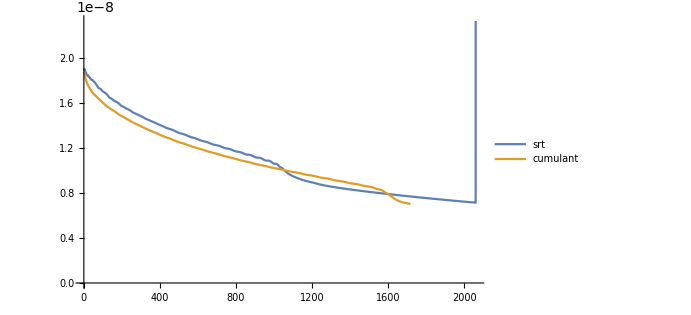

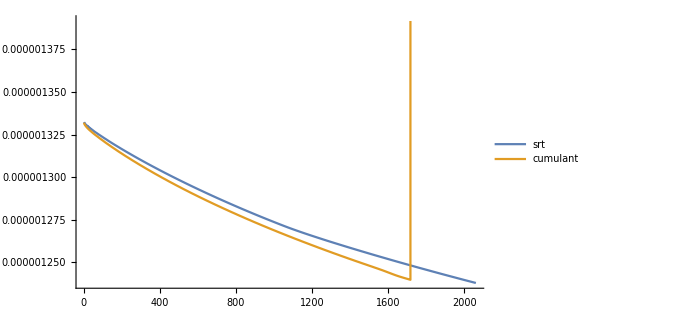

```mathematica
input = 2;

srts256
cumulants256

enstrophySRT = Flatten[ Take[#,1]&/@srt256Input[[input]]];
tkeSRT = Flatten[Drop[#,1]&/@srt256Input[[input]]];

enstrophyCumulant = Flatten[ Take[#,1]&/@cumulant256Input[[input]]];
tkeCumulant = Flatten[Drop[#,1]&/@cumulant256Input[[input]]];

ListLinePlot[{enstrophySRT,enstrophyCumulant}, PlotLegends->Placed[{"srt","cumulant"},{Right,Top}]]
ListLinePlot[{tkeSRT,tkeCumulant}, PlotLegends->Placed[{"srt","cumulant"},{Right,Top}]]
```

{srt_Re1000_size128,srt_Re2000_size128,srt_Re5000_size128,srt_Re10000_size128,srt_Re100000_size128}

{cumulant_Re1000_size128,cumulant_Re2000_size128,cumulant_Re5000_size128,cumulant_Re10000_size128,cumulant_Re100000_size128}

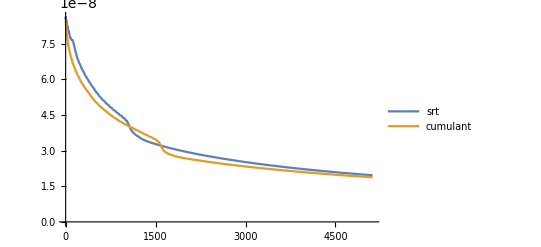

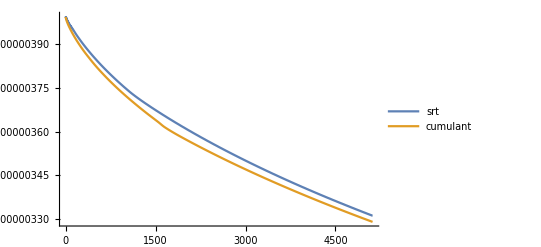

```mathematica
input = 3;

srts128
cumulants128

enstrophySRT = Flatten[ Take[#,1]&/@srt128Input[[input]]];
tkeSRT = Flatten[Drop[#,1]&/@srt128Input[[input]]];

enstrophyCumulant = Flatten[ Take[#,1]&/@cumulant128Input[[input]]];
tkeCumulant = Flatten[Drop[#,1]&/@cumulant128Input[[input]]];

ListLinePlot[{enstrophySRT,enstrophyCumulant}, PlotLegends->Placed[{"srt","cumulant"},{Right,Top}]]
ListLinePlot[{tkeSRT,tkeCumulant}, PlotLegends->Placed[{"srt","cumulant"},{Right,Top}]]
```

{srt_Re1000_size96,srt_Re2000_size96,srt_Re5000_size96,srt_Re6000_size96,srt_Re6100_size96,srt_Re6200_size96,srt_Re6300_size96,srt_Re6400_size96,srt_Re6500_size96,srt_Re7000_size96,srt_Re7500_size96,srt_Re8000_size96,srt_Re8500_size96,srt_Re9000_size96,srt_Re9500_size96,srt_Re10000_size96,srt_Re100000_size96}

{cumulant_Re1000_size96,cumulant_Re2000_size96,cumulant_Re5000_size96,cumulant_Re6000_size96,cumulant_Re6100_size96,cumulant_Re6200_size96,cumulant_Re6300_size96,cumulant_Re6400_size96,cumulant_Re6500_size96,cumulant_Re7000_size96,cumulant_Re7500_size96,cumulant_Re8000_size96,cumulant_Re8500_size96,cumulant_Re9000_size96,cumulant_Re9500_size96,cumulant_Re10000_size96,cumulant_Re100000_size96}

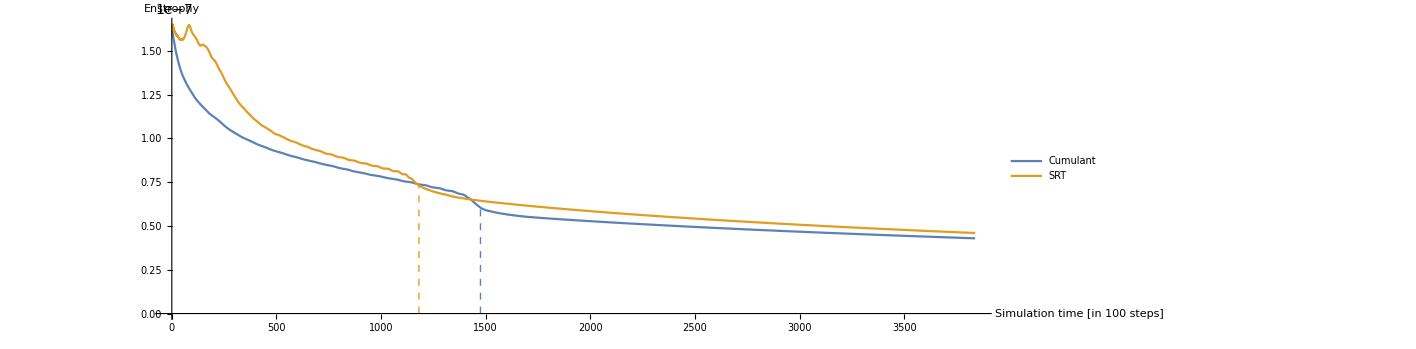

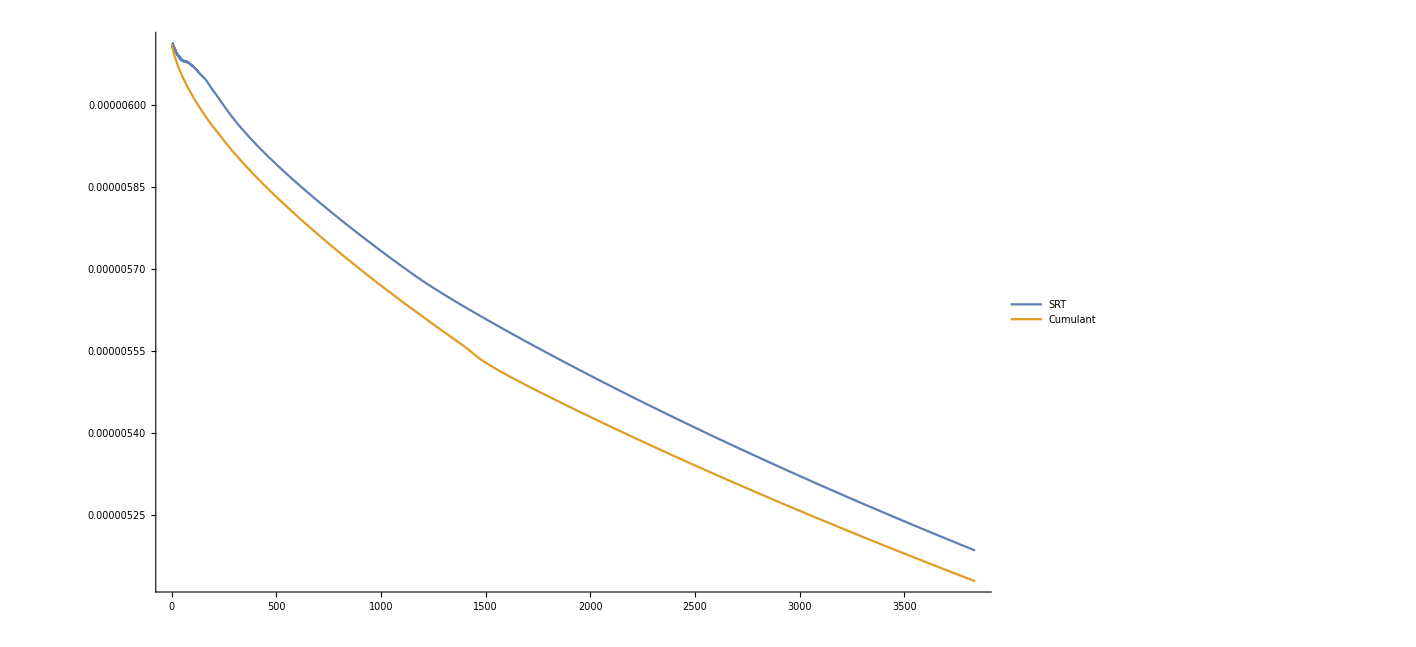

```mathematica
input = 4;

highlightCumulant=1475;
highlightSrt=1181;

srts96
cumulants96

enstrophySRT = Flatten[ Take[#,1]&/@srt96Input[[input]]];
tkeSRT = Flatten[Drop[#,1]&/@srt96Input[[input]]];

enstrophyCumulant = Flatten[ Take[#,1]&/@cumulant96Input[[input]]];
tkeCumulant = Flatten[Drop[#,1]&/@cumulant96Input[[input]]];

enstrophyPlot = ListLinePlot[{enstrophyCumulant,enstrophySRT}, PlotLegends->Placed[{"Cumulant","SRT"},{Right,Top}], AspectRatio->1/3,AxesLabel->{"Simulation time 
[in 100 steps]","Enstrophy"}];
cumulantLine=Line[{{highlightCumulant,0},{highlightCumulant,enstrophyCumulant[[highlightCumulant]]}}];
srtLine=Line[{{highlightSrt,0},{highlightSrt,enstrophySRT[[highlightSrt]]}}];
lines =Graphics[{ColorData[97,"ColorList"][[1]], Dashed,cumulantLine,ColorData[97,"ColorList"][[2]],srtLine}];
Show[enstrophyPlot,lines]
ListLinePlot[{tkeSRT,tkeCumulant}, PlotLegends->Placed[{"SRT","Cumulant"},{Right,Top}]]
```

```mathematica
ColorData[97,1]
```

RGBColor[0.368417, 0.506779, 0.709798]

{srt_Re1000_size96,srt_Re2000_size96,srt_Re5000_size96,srt_Re6000_size96,srt_Re6100_size96,srt_Re6200_size96,srt_Re6300_size96,srt_Re6400_size96,srt_Re6500_size96,srt_Re7000_size96,srt_Re7500_size96,srt_Re8000_size96,srt_Re8500_size96,srt_Re9000_size96,srt_Re9500_size96,srt_Re10000_size96,srt_Re100000_size96}

{cumulant_Re1000_size96,cumulant_Re2000_size96,cumulant_Re5000_size96,cumulant_Re6000_size96,cumulant_Re6100_size96,cumulant_Re6200_size96,cumulant_Re6300_size96,cumulant_Re6400_size96,cumulant_Re6500_size96,cumulant_Re7000_size96,cumulant_Re7500_size96,cumulant_Re8000_size96,cumulant_Re8500_size96,cumulant_Re9000_size96,cumulant_Re9500_size96,cumulant_Re10000_size96,cumulant_Re100000_size96}

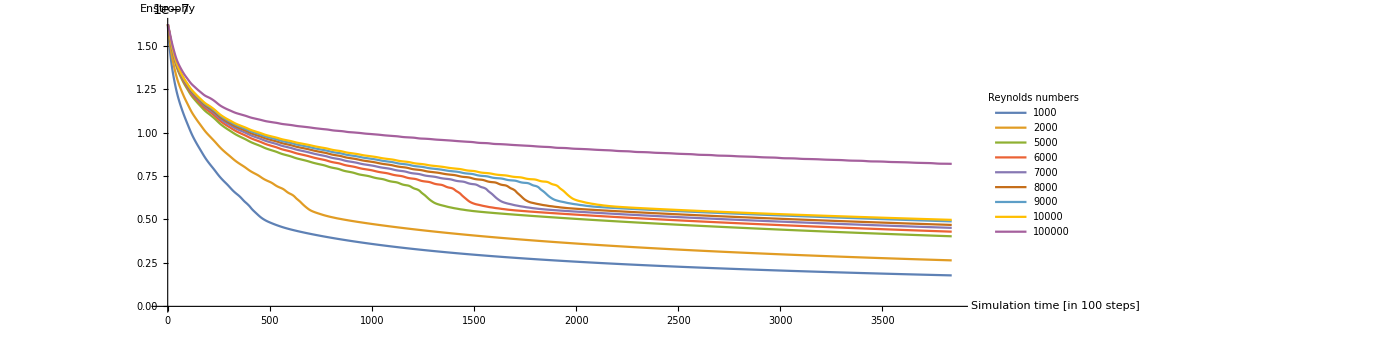

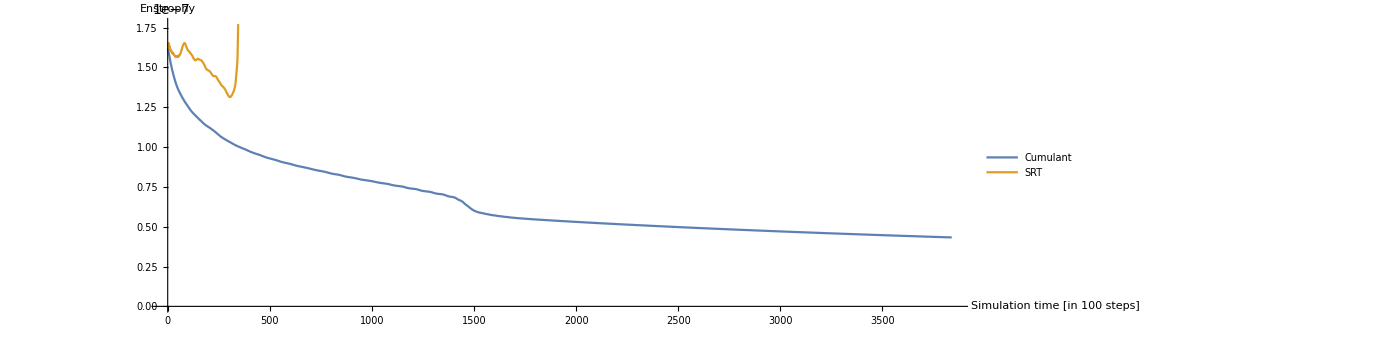

```mathematica
input = 5;

highlightCumulant=1475;
highlightSrt=1181;

srts96
cumulants96

enstrophySRT = Flatten[ Take[#,1]&/@srt96Input[[input]]];
tkeSRT = Flatten[Drop[#,1]&/@srt96Input[[input]]];

enstrophyCumulant = Flatten[ Take[#,1]&/@cumulant96Input[[input]]];
tkeCumulant = Flatten[Drop[#,1]&/@cumulant96Input[[input]]];

enstrophyCumulant1=Flatten[Take[#,1]&/@cumulant96Input[[1]]];
enstrophyCumulant2=Flatten[Take[#,1]&/@cumulant96Input[[2]]];
enstrophyCumulant3=Flatten[Take[#,1]&/@cumulant96Input[[3]]];
enstrophyCumulant4=Flatten[Take[#,1]&/@cumulant96Input[[4]]];

enstrophyCumulant5=Flatten[Take[#,1]&/@cumulant96Input[[10]]];
enstrophyCumulant6=Flatten[Take[#,1]&/@cumulant96Input[[12]]];
enstrophyCumulant7=Flatten[Take[#,1]&/@cumulant96Input[[14]]];
enstrophyCumulant8=Flatten[Take[#,1]&/@cumulant96Input[[16]]];
enstrophyCumulant9=Flatten[Take[#,1]&/@cumulant96Input[[17]]];

ListLinePlot[{enstrophyCumulant1,enstrophyCumulant2,enstrophyCumulant3,enstrophyCumulant4,enstrophyCumulant5,enstrophyCumulant6,enstrophyCumulant7,enstrophyCumulant8,enstrophyCumulant9}, PlotLegends->Placed[LineLegend[{1000, 2000, 5000, 6000, 7000, 8000, 9000, 10000, 100000}, LegendLabel->"Reynolds numbers",LegendLayout->{"Column",2}],{Right,Top}], AspectRatio->1/3,AxesLabel->{"Simulation time 
[in 100 steps]","Enstrophy"}
]

enstrophyPlot = ListLinePlot[{enstrophyCumulant,enstrophySRT}, PlotLegends->Placed[{"Cumulant","SRT"},{Right,Top}], AspectRatio->1/3,AxesLabel->{"Simulation time 
[in 100 steps]","Enstrophy"}];
cumulantLine=Line[{{highlightCumulant,0},{highlightCumulant,enstrophyCumulant[[highlightCumulant]]}}];
lines =Graphics[{cumulantLine}];

Show[enstrophyPlot]
```

```mathematica
ColorData[97,"ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]